```mathematica
(*
 First Setup f 

Assume f= aa x1 x2 + g(x3,...) 
*)
m=23; (* assume m=3(mod 4) *)
Mod[m,4]==3;
g={{2,1},{1,(m+1)/2}};
aa=-2;
nn=Length[g];
f={
{{{0,aa/2},{aa/2,0}},ConstantArray[0,{2,nn}]},
{ConstantArray[0,{nn,2}],g}}//ArrayFlatten;
f//MatrixForm;
vvnn2=Table[Subscript[x,i],{i,1,nn+2}];
(*
setting up inversive coordinate system 
*)
bb={1,0,0,0};
bb.f.bb;
bbhat={0,2,0,0};
bbhat.f.bbhat;
bbhat.f.bb;
bx={0,0,1/Sqrt[2],0};
bx.f.bx;
bx.f.bb;
bx.f.bbhat;
by={0,0,1,-2}/Sqrt[2m];
by.f.by//Simplify;
bx.f.by//Simplify;

{bb,bx,by,bbhat}.f.Transpose[{bb,bx,by,bbhat}]//Simplify//MatrixForm;

ga1[v_]:=v.f.bb/Sqrt[v.f.v]; (* bend *)
ga2[v_]:=v.f.bx/Sqrt[v.f.v];(* bx *) 
ga3[v_]:=v.f.by/Sqrt[v.f.v];  (* by *)
ga4[v_]:=v.f.bbhat/Sqrt[v.f.v];(* co bend *)

ga1p[v_]:=v.f.bb/Sqrt[-v.f.v]; (* recip height 1/z *)
ga2p[v_]:=v.f.bx/Sqrt[-v.f.v];(* x/z *) 
ga3p[v_]:=v.f.by/Sqrt[-v.f.v];  (* y/z *)
ga4p[v_]:=v.f.bbhat/Sqrt[-v.f.v];(* recip co height *)


invCoords[v_]:={ga1[v],
ga2[v],
ga3[v],
ga4[v]};
Rv[v_]:=IdentityMatrix[4]-2(Transpose[{(f.v)}].{v})/(v.f.v);

showCirc[circ_]:=If[Abs[N[ga1[circ]]]>10^(-15),
Circle[{ga2[circ],ga3[circ]}/ga1[circ],Abs[1/ga1[circ] ] ]
,
Line[
{
ga4[circ]/2{ga2[circ],ga3[circ]}-1000{-ga3[circ],ga2[circ]}
,
ga4[circ]/2{ga2[circ],ga3[circ]}+1000{-ga3[circ],ga2[circ]}
}
]
];
showCirc3D[circ_]:=If[Abs[N[ga1[circ]]]>10^(-15),
BSplineCurve[Map[(#+{ga2[circ],ga3[circ],0}/ga1[circ])&,{{0,-1,0},{1,-1,0},{1,1,0},{0,1,0},{-1,1,0},{-1,-1,0},{0,-1,0}}Abs[N[1/ga1[circ] ] ]],SplineWeights->{1,.5,.5,1,.5,.5,1},SplineKnots->{0,0,0,1/4,1/2,1/2,3/4,1,1,1}]
,
Line[
{
ga4[circ]/2{ga2[circ],ga3[circ],0}-1000{-ga3[circ],ga2[circ],0}
,
ga4[circ]/2{ga2[circ],ga3[circ],0}+1000{-ga3[circ],ga2[circ],0}
}
]
];
showPt[circ_]:=
Point[{ga2p[circ],ga3p[circ],1}/ga1p[circ]
];
showSph[circ_]:=If[Abs[N[ga1[circ]]]>10^(-15),
Sphere[
{ga2[circ],ga3[circ],0}/ga1[circ],Abs[1/ga1[circ] ] ] 
,
Polygon[
{
ga4[circ]/2{ga2[circ],ga3[circ],0}-1000{-ga3[circ],ga2[circ],0}
,
{ga4[circ]/2ga2[circ],ga4[circ]/2ga3[circ],100}-{-1000ga3[circ],1000ga2[circ],100}
,
{ga4[circ]/2ga2[circ],ga4[circ]/2ga3[circ],100}+{-1000ga3[circ],1000ga2[circ],100}
,
ga4[circ]/2{ga2[circ],ga3[circ],0}+1000{-ga3[circ],ga2[circ],0}
}
]
];
```

```mathematica
setOfVs={{0,0,-1,0},{1,0,1,0},{0,0,1,-2},{23,0,-1,2},{-1,1,0,0},{5,1,0,1},{9,7,2,3},{13,7,-2,4},{10,10,1,4},{21,10,-1,6},{13,11,-2,5},{21,11,2,6},{15,14,-1,6},{28,14,1,8},{23,16,-3,8},{26,16,3,8},{29,22,3,10},{38,22,-3,12},{29,25,0,11},{47,25,0,14},{33,27,2,12},{49,27,-2,15},{43,29,4,14},{45,29,-4,15},{44,34,-3,16},{59,34,3,18},{51,37,-4,18},{61,37,4,19},{49,39,-2,18},{69,39,2,21}}
```

{{0,0,-1,0},{1,0,1,0},{0,0,1,-2},{23,0,-1,2},{-1,1,0,0},{5,1,0,1},{9,7,2,3},{13,7,-2,4},{10,10,1,4},{21,10,-1,6},{13,11,-2,5},{21,11,2,6},{15,14,-1,6},{28,14,1,8},{23,16,-3,8},{26,16,3,8},{29,22,3,10},{38,22,-3,12},{29,25,0,11},{47,25,0,14},{33,27,2,12},{49,27,-2,15},{43,29,4,14},{45,29,-4,15},{44,34,-3,16},{59,34,3,18},{51,37,-4,18},{61,37,4,19},{49,39,-2,18},{69,39,2,21}}

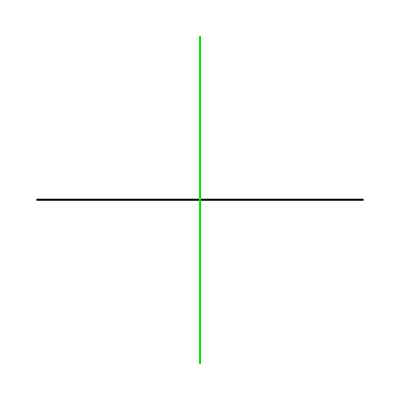

```mathematica
Show[Graphics[{showCirc/@setOfVs,Green,showCirc/@{setOfVs[[1]],setOfVs[[2]]}}],PlotRange->5]
```

```mathematica
showCirc/@{setOfVs[[1]],setOfVs[[2]]}
```

{Line[{{0,1000},{0,-1000}}],Line[{{-1/(√2),-1000},{-1/(√2),1000}}]}

```mathematica
showCirc/@{setOfVs[[3]],setOfVs[[4]]}
```

{Line[{{1000,0},{-1000,0}}],Line[{{-1000,√(23/2)},{1000,√(23/2)}}]}

```mathematica
(* Choose nice base pt *)
w0=vvnn2/.Solve[showPt[vvnn2][[1]]=={-1/(2Sqrt[2]), Sqrt[m/2]/2,2},vvnn2][[1]]/.Subscript[x, 4]->-1
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{-7,-2,0,-1}

```mathematica
w0.f.w0
showPt[w0]//Simplify
```

-16

Point[{-1/(2 √2),(√(23/2))/2,2}]

```mathematica
Show[Graphics3D[{Blue,Opacity[0.5],showSph/@setOfVs}],
Graphics3D[{Red,Opacity[1],showCirc3D/@setOfVs,showPt[w0],showPt[w0.Rv[setOfVs[[1]]]],showPt[w0.Rv[setOfVs[[3]]]]
,showPt[w0.Rv[setOfVs[[6]]]]
}],
Graphics3D[{Yellow,Opacity[1],Polygon[{
{-10,-10,0},
{10,-10,0},
{10,10,0},
{-10,10,0}
}]}],
PlotRange->{{-3,2},{-2,6},{0,2}}]
```

-Graphics3D-

```mathematica
g1={{26,12,2,7},{27,12,3,7},{-5,-1,0,-1},{-129,-58,-12,-34}};
g2={{27,16,4,8},{36,23,6,11},{-1,0,-1,0},{-150,-92,-24,-45}};
g3=Inverse[g2].g1;
```

```mathematica
wallToW0[w_]:=vvnn2/.Solve[w==w0.Rv[vvnn2],vvnn2][[1]]/.Subscript[x, 4]->1/.Subscript[x, 3]->1/.Subscript[x, 2]->1/.Subscript[x, 1]->1;
```

```mathematica
Show[
Graphics3D[{Blue,Opacity[.8],showSph/@Take[setOfVs,6],Orange,showSph/@{wallToW0[w0.g1],wallToW0[w0.Inverse[g1]]},Green,showSph/@{wallToW0[w0.g3],
wallToW0[w0.Inverse[g3]]}}],
Graphics3D[{Yellow,Opacity[.8],Polygon[{
{-10,-10,0},
{10,-10,0},
{10,10,0},
{-10,10,0}
}]}],
PlotRange->{{-3,2},{-2,6},{0,3}}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

-Graphics3D-

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

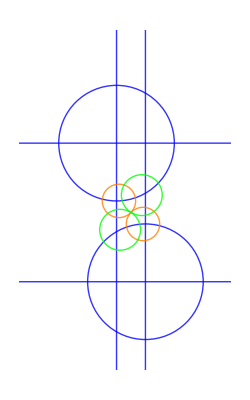

```mathematica
Show[
Graphics[{Thick,Blue,Opacity[.8],showCirc/@Take[setOfVs,6],Orange,showCirc/@{wallToW0[w0.g1],wallToW0[w0.Inverse[g1]]},Green,showCirc/@{wallToW0[w0.g3],
wallToW0[w0.Inverse[g3]]}}],
PlotRange->{{-3,2},{-2,6}}]
```

```mathematica
cluster={-setOfVs[[3]],-setOfVs[[4]]};
ga1[cluster[[1]].g1]>0
ga1[cluster[[2]].g1]>0
Smat={Rv[setOfVs[[1]]],
Rv[setOfVs[[2]]],
Rv[setOfVs[[5]]],
Rv[setOfVs[[6]]],
g1,
Inverse[g1],
g3,
Inverse[g3]
};
MatrixForm/@Smat
```

True

True

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | -1 | 1),(1 | 0 | 0 | 0
1 | 1 | 1 | 0
-2 | 0 | -1 | 0
-1 | 0 | -1 | 1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(6 | 1 | 0 | 1
25 | 6 | 0 | 5
-5 | -1 | 1 | -1
-60 | -12 | 0 | -11),(26 | 12 | 2 | 7
27 | 12 | 3 | 7
-5 | -1 | 0 | -1
-129 | -58 | -12 | -34),(12 | 12 | -2 | 5
27 | 26 | -3 | 11
-13 | -11 | 2 | -5
-87 | -86 | 12 | -36),(18 | 8 | -2 | 5
18 | 8 | -3 | 5
-13 | -7 | 2 | -4
-87 | -38 | 12 | -24),(8 | 8 | 2 | 3
18 | 18 | 3 | 7
1 | -1 | 0 | 0
-57 | -58 | -12 | -22)}

```mathematica
morecircs[from_,level_]:=If[level<levelmax,
Module[{j},For[j=1,j≤Length[Smat],j++,
w=Simplify[w.Smat⟦j⟧];
If[(0<=ga1[w] <sizemax  && !MemberQ[pic,w]),

AppendTo[pic,w];

morecircs[j,level+1];
];
w=w.Inverse[Smat⟦j⟧];
]
]
];
```

```mathematica
sizemax=50;
levelmax=60;

AllPics=Table[{},{k,1,Length[cluster]}];


For[k=1,k≤Length[cluster],k++,
pic={};

w=cluster[[k]];

Print[Timing[
morecircs[0,1];
]];

Print["Done with k=",k," out of ",Length[cluster]];
AllPics[[k]]=Union[pic];
Print[Length[Union[pic]]];
];
```

{2.31503,Null}

Done with k=1 out of 2

1617

{2.26813,Null}

Done with k=2 out of 2

1617

```mathematica
Pics=Union[Flatten[AllPics,1]];
Length[%]
```

3234

```mathematica
showText[circ_]:=If[N[ga1[circ]]>10^(-1),
Text[
Style[
Simplify[Abs[ga1[circ]/Sqrt[m/2]] ]
, 50./Abs[ga1[circ]]]
 ,N[ {ga2[circ],ga3[circ]}/ga1[circ]]]
,
{PointSize[0],Point[{0,0}]}
];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

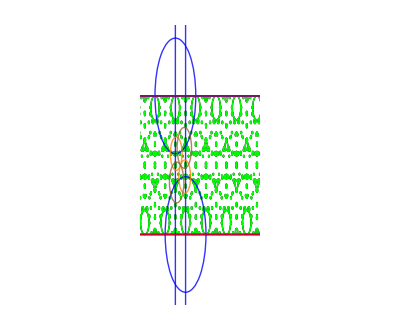

```mathematica
packPic=Show[
Graphics[showText/@(Pics)],

Graphics[showCirc/@(Pics)],
Graphics[{Green,Thick,showCirc/@(Join[AllPics[[1]],AllPics[[2]]])}],
Graphics[{Blue,Thick,showCirc/@cluster}],

Graphics[{Blue,Opacity[.8],showCirc/@Take[setOfVs,6],Orange,showCirc/@{wallToW0[w0.g1],wallToW0[w0.Inverse[g1]]},Brown,showCirc/@{wallToW0[w0.g3],
wallToW0[w0.Inverse[g3]]},Red,showCirc[setOfVs[[3]]],showCirc[setOfVs[[4]]]}],

PlotRange->{{-3,5},{-1.6,5}}]
```

```mathematica
(* Try moving infinity to get better pic? *)
```

```mathematica
g1wall=wallToW0[w0.g1];
g1iWall=wallToW0[w0.Inverse[g1]];
g3wall=wallToW0[w0.g3];
g3iWall=wallToW0[w0.Inverse[g3]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
move=IdentityMatrix[4].g1.Rv[setOfVs[[3]]].Inverse[g1];
(*move=Rv[setOfVs[[3]].move];*)
Show[
Graphics[{Thick,Blue,Opacity[.8],showCirc/@Take[setOfVs.move,6],Orange,showCirc/@{g1wall.move,g1iWall.move},Green,showCirc/@{g3wall.move,g3iWall.move
},Red,showCirc/@{setOfVs[[3]].move,setOfVs[[4]].move}}],
PlotRange->(ran={{-.102,-.10009},{1.4091,1.4125}})]
```

-Graphics-

```mathematica
cluster={-setOfVs[[3]].move,-setOfVs[[4]].move};
ga1[cluster[[1]].g1]>0
ga1[cluster[[2]].g1]>0
Smat={Rv[setOfVs[[1]].move],
Rv[setOfVs[[2]].move],
Rv[setOfVs[[5]].move],
Rv[setOfVs[[6]].move],
Inverse[move].g1.move,
Inverse[Inverse[move].g1.move],
Inverse[move].g3.move,
Inverse[Inverse[move].g3.move]
};
MatrixForm/@Smat
```

True

True

{(25922 | 25921 | -3703 | 10787
25921 | 25922 | -3703 | 10787
-3381 | -3381 | 484 | -1407
-125741 | -125741 | 17963 | -52326),(934123 | 933156 | -126546 | 388332
935089 | 934123 | -126677 | 388734
-135380 | -135240 | 18341 | -56280
-4538131 | -4533438 | 614783 | -1886585),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1666678 | 1661521 | -226864 | 692193
1671849 | 1666678 | -227568 | 694341
-239205 | -238465 | 32561 | -99345
-8104524 | -8079452 | 1103168 | -3365915),(79721 | 79707 | -10881 | 33158
80688 | 80673 | -11012 | 33560
-12080 | -12076 | 1649 | -5024
-389588 | -389517 | 53172 | -162039),(80673 | 79707 | -10635 | 33346
80688 | 79721 | -10636 | 33352
-11536 | -11396 | 1521 | -4768
-391708 | -387015 | 51636 | -161911),(53631 | 53138 | -7401 | 22209
53792 | 53299 | -7424 | 22276
-8316 | -8241 | 1147 | -3444
-260976 | -258581 | 36016 | -108073),(53299 | 53138 | -6943 | 22127
53792 | 53631 | -7008 | 22332
-7428 | -7407 | 967 | -3084
-259888 | -259107 | 33856 | -107893)}

```mathematica
morecircs[from_,level_]:=If[level<levelmax,
Module[{j},For[j=1,j≤Length[Smat],j++,
w=Simplify[w.Smat⟦j⟧];
If[(0<=ga1[w] <sizemax  && !MemberQ[pic,w]),

AppendTo[pic,w];

morecircs[j,level+1];
];
w=w.Inverse[Smat⟦j⟧];
]
]
];
```

```mathematica
sizemax=5000;
levelmax=60;

AllPics=Table[{},{k,1,Length[cluster]}];


For[k=1,k≤Length[cluster],k++,
pic={};

w=cluster[[k]];

Print[Timing[
morecircs[0,1];
]];

Print["Done with k=",k," out of ",Length[cluster]];
AllPics[[k]]=Union[pic];
Print[Length[Union[pic]]];
];
```

{0.091029,Null}

Done with k=1 out of 2

50

{0.114782,Null}

Done with k=2 out of 2

60

```mathematica
Pics=Union[Flatten[AllPics,1]];
Length[%]
```

110

```mathematica
showText[circ_]:=If[N[ga1[circ]]>10^(-1),
Text[
Style[
Simplify[Abs[ga1[circ]/Sqrt[m/2]] ]
, 50./Abs[ga1[circ]]]
 ,N[ {ga2[circ],ga3[circ]}/ga1[circ]]]
,
{PointSize[0],Point[{0,0}]}
];
```

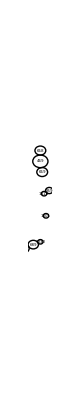

```mathematica
packPic=Show[
Graphics[showText/@(Pics)],

Graphics[showCirc/@(Pics)],

PlotRange->{{-.102,-.10009},{1.401,1.4125}}]
```

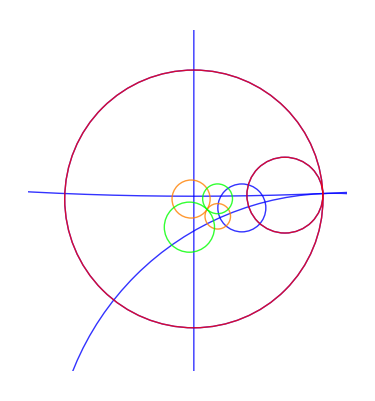

```mathematica
move=Rv[setOfVs[[3]]].g1;
(*move=Rv[setOfVs[[3]].move];*)
bckndPic=Show[
Graphics[{Thick,Blue,Opacity[.8],showCirc/@Take[setOfVs.move,6],Orange,showCirc/@{g1wall.move,g1iWall.move},Green,showCirc/@{g3wall.move,g3iWall.move
},Red,showCirc/@{setOfVs[[3]].move,setOfVs[[4]].move}}],
PlotRange->(ran={{-.78,-0.64},{1.9,2.05}})]
```

```mathematica
cluster={-setOfVs[[3]].move,-setOfVs[[4]].move};
ga1[cluster[[1]]]>0
ga1[cluster[[2]]]>0
Smat={Rv[setOfVs[[1]].move],
Rv[setOfVs[[2]].move],
Rv[setOfVs[[5]].move],
Rv[setOfVs[[6]].move],
Inverse[move].g1.move,
Inverse[Inverse[move].g1.move],
Inverse[move].g3.move,
Inverse[Inverse[move].g3.move]
};
MatrixForm/@Smat
```

False

True

{(6 | 1 | 0 | 1
25 | 6 | 0 | 5
-5 | -1 | 1 | -1
-60 | -12 | 0 | -11),(232 | 121 | 22 | 66
441 | 232 | 42 | 126
-210 | -110 | -19 | -60
-1554 | -814 | -148 | -443),(1 | 0 | 0 | 0
1 | 1 | 1 | 0
-2 | 0 | -1 | 0
-1 | 0 | -1 | 1),(36250 | 16641 | 3225 | 9675
78961 | 36250 | 7025 | 21075
-35125 | -16125 | -3124 | -9375
-259925 | -119325 | -23125 | -69374),(89381 | 41067 | 8277 | 23822
196608 | 90333 | 18208 | 52400
-89360 | -41056 | -8275 | -23816
-643232 | -295539 | -59568 | -171435),(90333 | 41067 | 8571 | 23914
196608 | 89381 | 18656 | 52048
-88816 | -40376 | -8427 | -23512
-647008 | -294141 | -61392 | -171283),(60117 | 27378 | 5475 | 15961
131072 | 59693 | 11936 | 34800
-60112 | -27377 | -5475 | -15960
-430624 | -196113 | -39216 | -114331),(59693 | 27378 | 5757 | 15863
131072 | 60117 | 12640 | 34832
-58672 | -26911 | -5659 | -15592
-429536 | -197007 | -41424 | -114147)}

```mathematica
morecircs[from_,level_]:=If[level<levelmax,
Module[{j},For[j=1,j≤Length[Smat],j++,
w=Simplify[w.Smat⟦j⟧];
If[(0<=ga1[w] <sizemax  && !MemberQ[pic,w]),

AppendTo[pic,w];

morecircs[j,level+1];
];
w=w.Inverse[Smat⟦j⟧];
]
]
];
```

```mathematica
sizemax=10000;
levelmax=80;

AllPics=Table[{},{k,1,Length[cluster]}];


For[k=1,k≤Length[cluster],k++,

w=cluster[[k]];
pic={w};

Print[Timing[
morecircs[0,1];
]];

Print["Done with k=",k," out of ",Length[cluster]];
AllPics[[k]]=Union[pic];
Print[Length[Union[pic]]];
];
```

{8.13053,Null}

Done with k=1 out of 2

1510

{11.2475,Null}

Done with k=2 out of 2

1775

```mathematica
Pics=Union[Flatten[AllPics,1]];
Length[%]
```

3285

```mathematica
showText[circ_]:=If[N[ga1[circ]]>10^(-1),
Text[
Style[
Simplify[Abs[ga1[circ]/Sqrt[m/2]] ]
, 3000./Abs[ga1[circ]]]
 ,N[ {ga2[circ],ga3[circ]}/ga1[circ]]]
,
{PointSize[0],Point[{0,0}]}
];
```

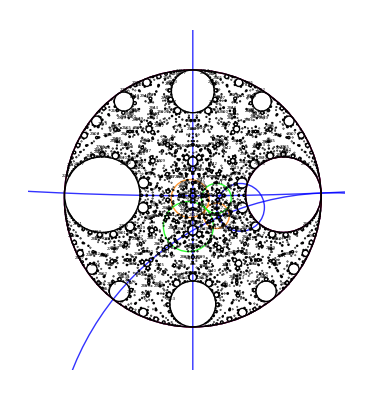

```mathematica
packPic=Show[bckndPic,
Graphics[showText/@(Pics)],

Graphics[showCirc/@(Pics)],

PlotRange->ran]
```